Numerov matrix method with  Lennard-Jones potential

```mathematica
(* Potential, desired max energy *)

V[s_]:=1/2 m ω^2 s^2;ϵm=100.;
(* Determine grid *)
rturn=FindRoot[V[s]==ϵm,{s,ϵm}]⟦1,2⟧;d=1/(√(2ϵm));
n=Round[2(rturn/d+4π )];s=Table[-(d (n+1))/2+d i,{i,n}];
(* Calculate KE matrix *)
𝕀[n_,d_]:=DiagonalMatrix[1+0Range[n-Abs[d]],d];
B=1./12(𝕀[n,-1]+10 𝕀[n,0]+𝕀[n,1]);
A=1/d^2(𝕀[n,-1]-2 𝕀[n,0]+𝕀[n,1]);
KE=-1/2 Inverse[B].A;
(* Hamiltonian *)
H=KE+DiagonalMatrix[V[s]];
(* Energies, wavefunctions *)
{eval,evec}=Eigensystem[H];
```

```mathematica
(* Swap list ordering and show first 20 eigenvalues *)
in=Ordering[eval];
```

```mathematica
eval=eval⟦in⟧;evec=evec⟦in⟧;
```

```mathematica
eval⟦;;20⟧
```

{0.05,0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95}

```mathematica
Integrate[psia[x,plotn]^2,{x,-∞,∞}]
```

1

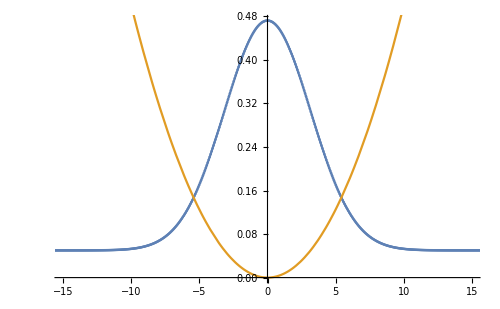

```mathematica
(* Construct and plot analytical wavefunctions *)
plotn=0; 
psia[s_,n_]:=((m ω)/(π ℏ))^(1/4)1/(√(2^n n!))Exp[-(m ω)/(2 ℏ)s^2]*HermiteH[n,√((m ω)/ℏ)s];
analytical=Plot[{psia[s,plotn]+ℏ ω (plotn+1/2), V[s]},{s,-60,60}];
(* Plot Numerov wavefunctions, normalize to 1 *)
f[i_]:=(-(d (n+1)))/2 +d i
scale=Map[f,Range[Length[evec[[plotn+1]]]]];
result=Transpose[{scale,(evec[[plotn+1]]/(√d)+eval[[plotn+1]])}];
numerov=ListPlot[result,PlotRange->{{-15, 15},Full}];
Show[numerov,analytical,ImageSize->500]
```